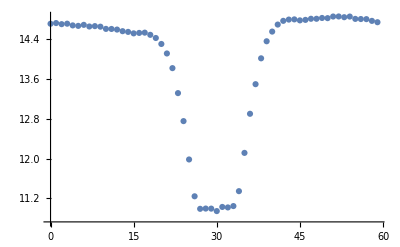

```mathematica
(*data = Import["/home/artem/projects/solver/build/trace/gloss_curve.txt", "Data"]//Flatten;*)
data = Import["/home/artem/projects/data_claster/trace/gloss_curve.txt", "Data"]//Flatten;
curve=Table[{i-2,data[[i]]}, {i,2,data[[1]]+1}];
ListPlot[curve]
```